```mathematica
Needs["PhysicalConstants`"]
ℏ=PlanckConstantReduced;
c=SpeedOfLight;
Subscript[k, B]=BoltzmannConstant;
T=300. Kelvin;
```

```mathematica
Subscript[λ, T]=ℏ c/(Subscript[k, B] T)
Subscript[λ, P]=2.*Pi*c/Subscript[ω, p]
```

7.63294×10^-6 Meter

(1.88365×10^9 Meter)/(Second ω_p)

```mathematica
ωp[ρ_,mc_,A_]:=Block[{q,ϵ,me,mp},
q=1.602*^-19;
ϵ=8.85*^-12;
me=9.10938291*^-31;
mp=1.79*^-27;
Sqrt[ρ q^2/(ϵ mc me mp A)]
]
```

```mathematica
ωp[19300,1,200]
ωp[2648,1,60]
```

1.31004×10^16

8.85938×10^15

```mathematica
ℏ
```

1.05457×10^-34 Joule Second

```mathematica
Ep[ω_,ωp_,γr_]:=Block[{},1+(ωp^2)/(ω(ω+γr*ωp))]
```

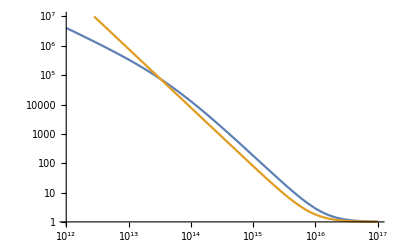

```mathematica
LogLogPlot[{Ep[ω,1.37*^16,3.3*^-3],Ep[ω,8.86*^15,0]},{ω,10^12,10^17},PlotRange->{{10^12,10^17},{1,10^7}}]
```

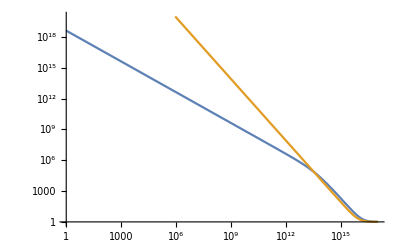

```mathematica
LogLogPlot[{Ep[ω,1.37*^16,3.3*^-3],Ep[ω,8.86*^15,0]},{ω,1,10^17},PlotRange->{{1,10^17},{1,10^20}}]
```

```mathematica
1+(ωp^2)/(ω(ω+γ))
```

1+ωp^2/(ω (γ+ω))

```mathematica
2.183*Pi*2
```

13.7162

```mathematica
1.37*^16*3.3*^-3
```

4.521×10^13

```mathematica
45/2./Pi
```

7.16197